```mathematica
Integrate[(R-x)^(3/2),{x,xo,R},Assumptions->{x∈Reals,R∈Reals}]//FullSimplify
```

2/5 (R-xo)^(5/2)

```mathematica
Integrate[1,{x,xo,R},Assumptions->{x∈Reals,R∈Reals}]//FullSimplify
```

R-xo

```mathematica
2/7 (-x^(7/2)+L^3 √(L+x)+3 L^2 x √(L+x)+3 L x^2 √(L+x)+x^3 √(L+x))//Simplify
```

2/7 (-x^(7/2)+L^3 √(L+x)+3 L^2 x √(L+x)+3 L x^2 √(L+x)+x^3 √(L+x))

```mathematica
Integrate[(R-x*Sin[θ]-h)^(3/2),{x,0,L},Assumptions->{L>0,h<R,h>0,θ>0,θ<π/2,x∈Reals,R∈Reals}]
```

-2/5 Csc[θ] (L Sin[θ] √(-h+R-L Sin[θ]) (2 h-2 R+L Sin[θ])-(h-R)^2 (√(-h+R)-√(-h+R-L Sin[θ])))

```mathematica
2/5 (-h+R)^(5/2) Sec[]
```

```mathematica
Sec[π/2-0.0001]
```

10000.

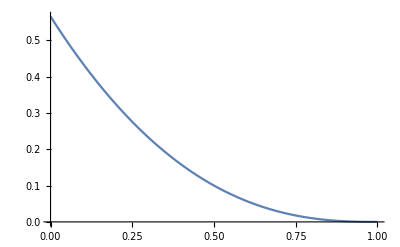

```mathematica
θ=π/4;
R=1;
Plot[2/5 (-h+R)^(5/2) Csc[θ],{h,0,R}]
```

```mathematica
2/5 (-h+R)^(5/2)
```

```mathematica
Csc[0]
```

ComplexInfinity

```mathematica
Solve[(r-h)/Sin[θ]==L,
```

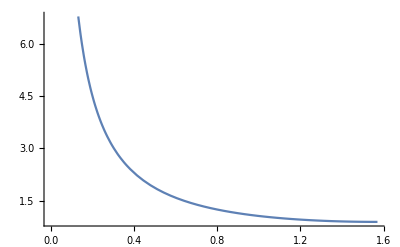

```mathematica
Plot[(R-0.1)/Sin[x],{x,0,π/2}]
```

```mathematica
L=3;
R=1;
θ=0.000002;
h=0.1;
-2/5 Csc[θ] (L Sin[θ] √(-h+R-L Sin[θ]) (2 h-2 R+L Sin[θ])-(h-R)^2 (√(-h+R)-√(-h+R-L Sin[θ])))
```

2.56143

```mathematica
-2/5 Csc[θ] (L Sin[θ] √(-h+R-L Sin[θ]) (2 h-2 R+L Sin[θ])-(h-R)^2 (√(-h+R)-√(-h+R-L Sin[θ])))//FullSimplify
```

-2/5 Csc[θ] (L Sin[θ] √(-h+R-L Sin[θ]) (2 h-2 R+L Sin[θ])-(h-R)^2 (√(-h+R)-√(-h+R-L Sin[θ])))

```mathematica
Limit[-2/5 Csc[θ] (L Sin[θ] √(-h+R-L Sin[θ]) (2 h-2 R+L Sin[θ])-(h-R)^2 (√(-h+R)-√(-h+R-L Sin[θ]))),θ->0]
```

L (-h+R)^(3/2)

```mathematica
{-1,0,0}×{0.97,0.03,0}
```

{0.,0.,-0.03}

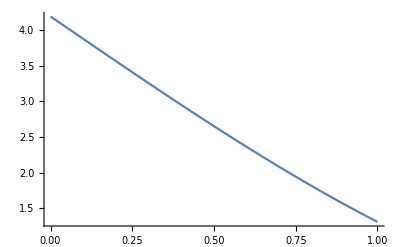

```mathematica
Plot[π/12(4+d)(2-d)^2,{d,0,1}]
```

```mathematica
π/12(4+d)(2-d)^2/.d->0
```

(4 π)/3

```mathematica
4. π/6
```

2.0944

```mathematica
R=1;
MPI=3.14;
L2=2;
d=2;
8.0*MPI*R*R*R/3.0+2*MPI*R*R*L2-MPI*(4*R+d)*(2*R-d)*(2*R-d)/12.0
```

20.9333

```mathematica
M_PI
```

M_PI

```mathematica
2*4*3.14/3+4*3.14
```

20.9333

```mathematica
Solve[V==2*(4/3 π*R^3+π*R^2*L2)-π/12(4*R+d)*(2*R-d)^2,d]
```

{{d→(12 2^(1/3) π R^2)/((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2))^(1/3))+((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2))^(1/3))/(3 2^(1/3) π)},{d→-(6 2^(1/3) (1+ⅈ √3) π R^2)/((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2))^(1/3))-((1-ⅈ √3) (648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2))^(1/3))/(6 2^(1/3) π)},{d→-(6 2^(1/3) (1-ⅈ √3) π R^2)/((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2))^(1/3))-((1+ⅈ √3) (648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2))^(1/3))/(6 2^(1/3) π)}}

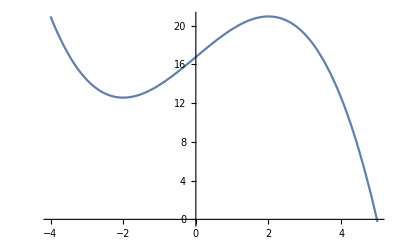

```mathematica
R=1;
L2=2;
Plot[2*(4/3 π*R^3+π*R^2*L2)-π/12(4*R+d)*(2*R-d)^2,{d,-4R,5*R}]
```

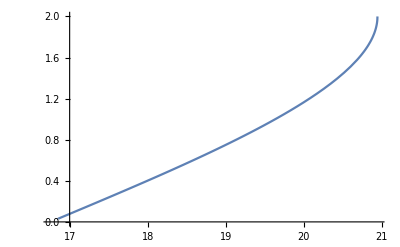

```mathematica
Plot[-(6 2^(1/3) (1-ⅈ √3) π R^2)/((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2))^(1/3))-((1+ⅈ √3) (648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2))^(1/3))/(6 2^(1/3) π),{V,(16 π)/3,(20 π)/3}]
```

```mathematica
2*(4/3 π*R^3+π*R^2*L2)-π/12(4*R+d)*(2*R-d)^2/.d->2*R
```

(20 π)/3

```mathematica
-(6 2^(1/3) (1-ⅈ √3) π R^2)/((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2))^(1/3))-((1+ⅈ √3) (648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2))^(1/3))/(6 2^(1/3) π)/.V->16*π/3.
```

-6.31503×10^-16+8.88178×10^-16 ⅈ

```mathematica
16*π/3.
```

16.7552

```mathematica
-(6 2^(1/3) (1-ⅈ √3) π R^2)/((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2))^(1/3))-((1+ⅈ √3) (648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2))^(1/3))/(6 2^(1/3) π)/.V->20*π/3.
```

2.+0. ⅈ

```mathematica
ComplexExpand[Re[-(6 2^(1/3) (1-ⅈ √3) π R^2)/((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2))^(1/3))-((1+ⅈ √3) (648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2))^(1/3))/(6 2^(1/3) π)]]
```

-((6 2^(1/3) π R^2 Cos[1/3 Arg[648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)]])/((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]])^2+√((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]]^2)^(1/6))-1/(6 2^(1/3) π)Cos[1/3 Arg[648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)]] ((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]])^2+√((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]]^2)^(1/6)+(6 2^(1/3) √3 π R^2 Sin[1/3 Arg[648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)]])/((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]])^2+√((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]]^2)^(1/6)+1/(2 2^(1/3) √3 π)((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]])^2+√((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]]^2)^(1/6) Sin[1/3 Arg[648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)]]

```mathematica
-((6 2^(1/3) π R^2 Cos[1/3 Arg[648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)]])/((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]])^2+√((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]]^2)^(1/6))-1/(6 2^(1/3) π)Cos[1/3 Arg[648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)]] ((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]])^2+√((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]]^2)^(1/6)+(6 2^(1/3) √3 π R^2 Sin[1/3 Arg[648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)]])/((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]])^2+√((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]]^2)^(1/6)+1/(2 2^(1/3) √3 π)((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]])^2+√((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]]^2)^(1/6) Sin[1/3 Arg[648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)]]//CForm
```

(-6*Power(2,0.3333333333333333)*Pi*Power(R,2)*
      Cos(Arg(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V + 
          Sqrt(-186624*Power(Pi,6)*Power(R,6) + 
            Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2)))/3.))/
    Power(Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V + 
        Power(Power(-186624*Power(Pi,6)*Power(R,6) + 
            Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2),2),0.25)*
         Cos(Arg(-186624*Power(Pi,6)*Power(R,6) + 
             Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2))/2.),2) + 
      Sqrt(Power(-186624*Power(Pi,6)*Power(R,6) + 
          Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2),2))*
       Power(Sin(Arg(-186624*Power(Pi,6)*Power(R,6) + 
            Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2))/2.),2),
     0.16666666666666666) - (Cos(Arg(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 
          324*Power(Pi,2)*V + Sqrt(-186624*Power(Pi,6)*Power(R,6) + 
            Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2)))/3.)*
      Power(Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V + 
          Power(Power(-186624*Power(Pi,6)*Power(R,6) + 
              Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2),2),0.25)*
           Cos(Arg(-186624*Power(Pi,6)*Power(R,6) + 
               Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2))/2.),2) + 
        Sqrt(Power(-186624*Power(Pi,6)*Power(R,6) + 
            Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2),2))*
         Power(Sin(Arg(-186624*Power(Pi,6)*Power(R,6) + 
              Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2))/2.),2),
       0.16666666666666666))/(6.*Power(2,0.3333333333333333)*Pi) + 
   (6*Power(2,0.3333333333333333)*Sqrt(3)*Pi*Power(R,2)*
      Sin(Arg(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V + 
          Sqrt(-186624*Power(Pi,6)*Power(R,6) + 
            Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2)))/3.))/
    Power(Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V + 
        Power(Power(-186624*Power(Pi,6)*Power(R,6) + 
            Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2),2),0.25)*
         Cos(Arg(-186624*Power(Pi,6)*Power(R,6) + 
             Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2))/2.),2) + 
      Sqrt(Power(-186624*Power(Pi,6)*Power(R,6) + 
          Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2),2))*
       Power(Sin(Arg(-186624*Power(Pi,6)*Power(R,6) + 
            Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2))/2.),2),
     0.16666666666666666) + (Power(Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 
          324*Power(Pi,2)*V + Power(Power(-186624*Power(Pi,6)*Power(R,6) + 
              Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2),2),0.25)*
           Cos(Arg(-186624*Power(Pi,6)*Power(R,6) + 
               Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2))/2.),2) + 
        Sqrt(Power(-186624*Power(Pi,6)*Power(R,6) + 
            Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2),2))*
         Power(Sin(Arg(-186624*Power(Pi,6)*Power(R,6) + 
              Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2))/2.),2),
       0.16666666666666666)*Sin(Arg(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 
          324*Power(Pi,2)*V + Sqrt(-186624*Power(Pi,6)*Power(R,6) + 
            Power(648*L2*Power(Pi,3)*Power(R,2) + 432*Power(Pi,3)*Power(R,3) - 324*Power(Pi,2)*V,2)))/3.))/
    (2.*Power(2,0.3333333333333333)*Sqrt(3)*Pi)

```mathematica
-((6 2^(1/3) π R^2 Cos[1/3 Arg[648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)]])/((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]])^2+√((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]]^2)^(1/6))-1/(6 2^(1/3) π)Cos[1/3 Arg[648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)]] ((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]])^2+√((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]]^2)^(1/6)+(6 2^(1/3) √3 π R^2 Sin[1/3 Arg[648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)]])/((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]])^2+√((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]]^2)^(1/6)+1/(2 2^(1/3) √3 π)((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]])^2+√((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]]^2)^(1/6) Sin[1/3 Arg[648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)]]/.L2->2/.R->1/.V->20
```

-2 Cos[1/3 (π+ArcTan[(√(186624 π^6-(-6480 π^2+1728 π^3)^2))/(-6480 π^2+1728 π^3)])]+2 √3 Sin[1/3 (π+ArcTan[(√(186624 π^6-(-6480 π^2+1728 π^3)^2))/(-6480 π^2+1728 π^3)])]

```mathematica
-((6 2^(1/3) π R^2 Cos[1/3 Arg[648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)]])/((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]])^2+√((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]]^2)^(1/6))-1/(6 2^(1/3) π)Cos[1/3 Arg[648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)]] ((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]])^2+√((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]]^2)^(1/6)+(6 2^(1/3) √3 π R^2 Sin[1/3 Arg[648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)]])/((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]])^2+√((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]]^2)^(1/6)+1/(2 2^(1/3) √3 π)((648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]])^2+√((-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2]]^2)^(1/6) Sin[1/3 Arg[648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V+√(-186624 π^6 R^6+(648 L2 π^3 R^2+432 π^3 R^3-324 π^2 V)^2)]]/.L2->2/.R->1
```

-((6 2^(1/3) π Cos[1/3 Arg[1728 π^3-324 π^2 V+√(-186624 π^6+(1728 π^3-324 π^2 V)^2)]])/((1728 π^3-324 π^2 V+((-186624 π^6+(1728 π^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6+(1728 π^3-324 π^2 V)^2]])^2+√((-186624 π^6+(1728 π^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6+(1728 π^3-324 π^2 V)^2]]^2)^(1/6))-1/(6 2^(1/3) π)Cos[1/3 Arg[1728 π^3-324 π^2 V+√(-186624 π^6+(1728 π^3-324 π^2 V)^2)]] ((1728 π^3-324 π^2 V+((-186624 π^6+(1728 π^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6+(1728 π^3-324 π^2 V)^2]])^2+√((-186624 π^6+(1728 π^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6+(1728 π^3-324 π^2 V)^2]]^2)^(1/6)+(6 2^(1/3) √3 π Sin[1/3 Arg[1728 π^3-324 π^2 V+√(-186624 π^6+(1728 π^3-324 π^2 V)^2)]])/((1728 π^3-324 π^2 V+((-186624 π^6+(1728 π^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6+(1728 π^3-324 π^2 V)^2]])^2+√((-186624 π^6+(1728 π^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6+(1728 π^3-324 π^2 V)^2]]^2)^(1/6)+1/(2 2^(1/3) √3 π)((1728 π^3-324 π^2 V+((-186624 π^6+(1728 π^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6+(1728 π^3-324 π^2 V)^2]])^2+√((-186624 π^6+(1728 π^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6+(1728 π^3-324 π^2 V)^2]]^2)^(1/6) Sin[1/3 Arg[1728 π^3-324 π^2 V+√(-186624 π^6+(1728 π^3-324 π^2 V)^2)]]

```mathematica
FullSimplify[-((6 2^(1/3) π Cos[1/3 Arg[1728 π^3-324 π^2 V+√(-186624 π^6+(1728 π^3-324 π^2 V)^2)]])/((1728 π^3-324 π^2 V+((-186624 π^6+(1728 π^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6+(1728 π^3-324 π^2 V)^2]])^2+√((-186624 π^6+(1728 π^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6+(1728 π^3-324 π^2 V)^2]]^2)^(1/6))-1/(6 2^(1/3) π)Cos[1/3 Arg[1728 π^3-324 π^2 V+√(-186624 π^6+(1728 π^3-324 π^2 V)^2)]] ((1728 π^3-324 π^2 V+((-186624 π^6+(1728 π^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6+(1728 π^3-324 π^2 V)^2]])^2+√((-186624 π^6+(1728 π^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6+(1728 π^3-324 π^2 V)^2]]^2)^(1/6)+(6 2^(1/3) √3 π Sin[1/3 Arg[1728 π^3-324 π^2 V+√(-186624 π^6+(1728 π^3-324 π^2 V)^2)]])/((1728 π^3-324 π^2 V+((-186624 π^6+(1728 π^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6+(1728 π^3-324 π^2 V)^2]])^2+√((-186624 π^6+(1728 π^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6+(1728 π^3-324 π^2 V)^2]]^2)^(1/6)+1/(2 2^(1/3) √3 π)((1728 π^3-324 π^2 V+((-186624 π^6+(1728 π^3-324 π^2 V)^2)^2)^(1/4) Cos[1/2 Arg[-186624 π^6+(1728 π^3-324 π^2 V)^2]])^2+√((-186624 π^6+(1728 π^3-324 π^2 V)^2)^2) Sin[1/2 Arg[-186624 π^6+(1728 π^3-324 π^2 V)^2]]^2)^(1/6) Sin[1/3 Arg[1728 π^3-324 π^2 V+√(-186624 π^6+(1728 π^3-324 π^2 V)^2)]]]
```

((2 2^(1/3) π^(2/3)+((16 π-3 V)^2+3 √((80 π^2-32 π V+3 V^2)^2)+2 √3 (16 π-3 V) ((80 π^2-32 π V+3 V^2)^2)^(1/4) Cos[1/2 Arg[80 π^2-32 π V+3 V^2]])^(1/3)) (-Cos[1/3 Arg[16 π-3 V+√(240 π^2-96 π V+9 V^2)]]+√3 Sin[1/3 Arg[16 π-3 V+√(240 π^2-96 π V+9 V^2)]]))/(2^(2/3) π^(1/3) ((16 π-3 V)^2+3 √((80 π^2-32 π V+3 V^2)^2)+2 √3 (16 π-3 V) ((80 π^2-32 π V+3 V^2)^2)^(1/4) Cos[1/2 Arg[80 π^2-32 π V+3 V^2]])^(1/6))

```mathematica
((2 2^(1/3) π^(2/3)+((16 π-3 V)^2+3 √((80 π^2-32 π V+3 V^2)^2)+2 √3 (16 π-3 V) ((80 π^2-32 π V+3 V^2)^2)^(1/4) Cos[1/2 Arg[80 π^2-32 π V+3 V^2]])^(1/3)) (-Cos[1/3 Arg[16 π-3 V+√(240 π^2-96 π V+9 V^2)]]+√3 Sin[1/3 Arg[16 π-3 V+√(240 π^2-96 π V+9 V^2)]]))/(2^(2/3) π^(1/3) ((16 π-3 V)^2+3 √((80 π^2-32 π V+3 V^2)^2)+2 √3 (16 π-3 V) ((80 π^2-32 π V+3 V^2)^2)^(1/4) Cos[1/2 Arg[80 π^2-32 π V+3 V^2]])^(1/6))//CForm
```

((2*Power(2,0.3333333333333333)*Power(Pi,0.6666666666666666) + 
       Power(Power(16*Pi - 3*V,2) + 3*Sqrt(Power(80*Power(Pi,2) - 32*Pi*V + 3*Power(V,2),2)) + 
         2*Sqrt(3)*(16*Pi - 3*V)*Power(Power(80*Power(Pi,2) - 32*Pi*V + 3*Power(V,2),2),0.25)*
          Cos(Arg(80*Power(Pi,2) - 32*Pi*V + 3*Power(V,2))/2.),0.3333333333333333))*
     (-Cos(Arg(16*Pi - 3*V + Sqrt(240*Power(Pi,2) - 96*Pi*V + 9*Power(V,2)))/3.) + 
       Sqrt(3)*Sin(Arg(16*Pi - 3*V + Sqrt(240*Power(Pi,2) - 96*Pi*V + 9*Power(V,2)))/3.)))/
   (Power(2,0.6666666666666666)*Power(Pi,0.3333333333333333)*
     Power(Power(16*Pi - 3*V,2) + 3*Sqrt(Power(80*Power(Pi,2) - 32*Pi*V + 3*Power(V,2),2)) + 
       2*Sqrt(3)*(16*Pi - 3*V)*Power(Power(80*Power(Pi,2) - 32*Pi*V + 3*Power(V,2),2),0.25)*
        Cos(Arg(80*Power(Pi,2) - 32*Pi*V + 3*Power(V,2))/2.),0.16666666666666666))

```mathematica
Solve[vol==(4/3 π*R^3+π*R^2 L),L]
```

{{L→(-4 π R^3+3 vol)/(3 π R^2)}}

```mathematica
(-4 π R^3+3 vol)/(3 π R^2)//CForm
```

(-4*Pi*Power(R,3) + 3*vol)/(3.*Pi*Power(R,2))

```mathematica
V=(4/3 π*R^3+π*R^2*L)*2-π/12(4*R+d)*(2*R-d)^2;
D[V,d]
DSolve[{π*R^2*L'[t]==a*(4/3 π*R^3+π*R^2*L[t]),L[0]==L1},L[t],t]
```

-1/12 π (-d+2 R)^2+1/6 π (-d+2 R) (d+4 R)

{{L[t]→1/3 (3 ⅇ^(a t) L1-4 R+4 ⅇ^(a t) R)}}

```mathematica
Solve[1/3 (3 ⅇ^(a t) L1-4 R+4 ⅇ^(a t) R)==2*L1,t]
```

{{t→ConditionalExpression[(2 ⅈ π C[1]+Log[(2 (3 L1+2 R))/(3 L1+4 R)])/a,C[1]∈Integers]}}

```mathematica
(2 (3 L1+2 R))/(3 L1+4 R)/.R->1/.L1->1
```

10/7

```mathematica
L[t]
```

L[t]

```mathematica
DSolve[{π*R^2*L'[t]==a*(4/3 π*R^3+π*R^2*L[t]),L[0]==L1},L[t],t]
```

```mathematica
V=(4/3 π*R^3+π*R^2*L)*2-π/12(4*R+d)*(2*R-d)^2;
D[V,d]
```

-1/12 π (-d+2 R)^2+1/6 π (-d+2 R) (d+4 R)

```mathematica
DSolve[{(-1/12 π (-d[t]+2 R)^2+1/6 π (-d[t]+2 R) (d[t]+4 R))*d'[t]==a*((4/3 π*R^3+π*R^2*L)*2-π/12(4*R+d[t])*(2*R-d[t])^2),d[0]==0},d[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

{{d[t]→(2 2^(1/3) R^2+2^(2/3) (3 L R^2-3 ⅇ^(a t) L R^2+2 R^3-2 ⅇ^(a t) R^3+1/216 √(-186624 R^6+(648 L R^2+432 R^3+216 ⅇ^(a t) (-3 L R^2-2 R^3))^2))^(2/3))/((3 L R^2-3 ⅇ^(a t) L R^2+2 R^3-2 ⅇ^(a t) R^3+1/216 √(-186624 R^6+(648 L R^2+432 R^3+216 ⅇ^(a t) (-3 L R^2-2 R^3))^2))^(1/3))},{d[t]→-((ⅈ (-2 ⅈ 2^(1/3) R^2-2 2^(1/3) √3 R^2-ⅈ 2^(2/3) (3 L R^2-3 ⅇ^(a t) L R^2+2 R^3-2 ⅇ^(a t) R^3+1/216 √(-186624 R^6+(648 L R^2+432 R^3+216 ⅇ^(a t) (-3 L R^2-2 R^3))^2))^(2/3)+2^(2/3) √3 (3 L R^2-3 ⅇ^(a t) L R^2+2 R^3-2 ⅇ^(a t) R^3+1/216 √(-186624 R^6+(648 L R^2+432 R^3+216 ⅇ^(a t) (-3 L R^2-2 R^3))^2))^(2/3)))/(2 (3 L R^2-3 ⅇ^(a t) L R^2+2 R^3-2 ⅇ^(a t) R^3+1/216 √(-186624 R^6+(648 L R^2+432 R^3+216 ⅇ^(a t) (-3 L R^2-2 R^3))^2))^(1/3)))},{d[t]→(ⅈ (2 ⅈ 2^(1/3) R^2-2 2^(1/3) √3 R^2+ⅈ 2^(2/3) (3 L R^2-3 ⅇ^(a t) L R^2+2 R^3-2 ⅇ^(a t) R^3+1/216 √(-186624 R^6+(648 L R^2+432 R^3+216 ⅇ^(a t) (-3 L R^2-2 R^3))^2))^(2/3)+2^(2/3) √3 (3 L R^2-3 ⅇ^(a t) L R^2+2 R^3-2 ⅇ^(a t) R^3+1/216 √(-186624 R^6+(648 L R^2+432 R^3+216 ⅇ^(a t) (-3 L R^2-2 R^3))^2))^(2/3)))/(2 (3 L R^2-3 ⅇ^(a t) L R^2+2 R^3-2 ⅇ^(a t) R^3+1/216 √(-186624 R^6+(648 L R^2+432 R^3+216 ⅇ^(a t) (-3 L R^2-2 R^3))^2))^(1/3))}}

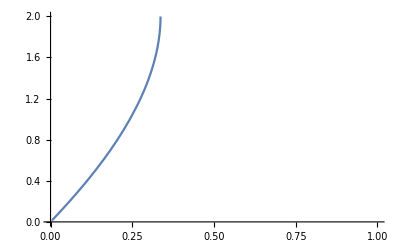

```mathematica
Plot[-((ⅈ (-2 ⅈ 2^(1/3) R^2-2 2^(1/3) √3 R^2-ⅈ 2^(2/3) (3 L R^2-3 ⅇ^(a t) L R^2+2 R^3-2 ⅇ^(a t) R^3+1/216 √(-186624 R^6+(648 L R^2+432 R^3+216 ⅇ^(a t) (-3 L R^2-2 R^3))^2))^(2/3)+2^(2/3) √3 (3 L R^2-3 ⅇ^(a t) L R^2+2 R^3-2 ⅇ^(a t) R^3+1/216 √(-186624 R^6+(648 L R^2+432 R^3+216 ⅇ^(a t) (-3 L R^2-2 R^3))^2))^(2/3)))/(2 (3 L R^2-3 ⅇ^(a t) L R^2+2 R^3-2 ⅇ^(a t) R^3+1/216 √(-186624 R^6+(648 L R^2+432 R^3+216 ⅇ^(a t) (-3 L R^2-2 R^3))^2))^(1/3)))/.R->1/.L->1/.a->1,{t,0,1}]
```

```mathematica
Solve[-((ⅈ (-2 ⅈ 2^(1/3) R^2-2 2^(1/3) √3 R^2-ⅈ 2^(2/3) (3 L R^2-3 ⅇ^(a t) L R^2+2 R^3-2 ⅇ^(a t) R^3+1/216 √(-186624 R^6+(648 L R^2+432 R^3+216 ⅇ^(a t) (-3 L R^2-2 R^3))^2))^(2/3)+2^(2/3) √3 (3 L R^2-3 ⅇ^(a t) L R^2+2 R^3-2 ⅇ^(a t) R^3+1/216 √(-186624 R^6+(648 L R^2+432 R^3+216 ⅇ^(a t) (-3 L R^2-2 R^3))^2))^(2/3)))/(2 (3 L R^2-3 ⅇ^(a t) L R^2+2 R^3-2 ⅇ^(a t) R^3+1/216 √(-186624 R^6+(648 L R^2+432 R^3+216 ⅇ^(a t) (-3 L R^2-2 R^3))^2))^(1/3)))==2,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→Log[(-1+3 R^2+3 L R^2+2 R^3)/(R^2 (3 L+2 R))]/a}}

```mathematica
Log[(-1+3 R^2+3 L R^2+2 R^3)/(R^2 (3 L+2 R))]/a
```

```mathematica
Log[(2*1*4/3*1)/(1+4/3)]
```

Log[8/7]

```mathematica
Log[8/7]/10.0
```

0.0133531

```mathematica
Log[2]/10.0
```

0.0693147

```mathematica
Log[8/7]/0.015
```

8.90209

```mathematica
Log[(-1+3 R^2+3 L R^2+2 R^3)/(R^2 (3 L+2 R))]/a
```

```mathematica
(-1+3 R^2+3 L R^2+2 R^3)/(R^2 (3 L+2 R))//CForm
```

(-1 + 3*Power(R,2) + 3*L*Power(R,2) + 2*Power(R,3))/(Power(R,2)*(3*L + 2*R))

```mathematica
(-1+3 R^2+3 L R^2+2 R^3)/(R^2 (3 L+2 R))/.R->1/.L->1
```

7/5

```mathematica
Log[7/5.]
```

0.336472